```mathematica
ClearAll["Global`*"];
```

```mathematica
v={0,0,0,0,0,0};
```

```mathematica
event={{{0},{1,1,1,1,1,1}},{{1},{0,1,1,1,1,2}},{{2},{0,0,1,1,2,2}},
{{2},{0,0,1,1,1,3}},{{3},{0,0,0,3,2,1}},{{3},{0,0,0,2,2,2}},
{{3},{0,0,0,1,1,4}},{{4},{0,0,0,0,5,1}},{{4},{0,0,0,0,4,2}},
{{4},{0,0,0,0,3,3}},{{5},{0,0,0,0,0,6}}};
```

```mathematica
For[i=1,i<6!,i++,event=Append[event,event[[1]]]];
For[i=1,i<(6!)^2/(2!4!),i++,event=Append[event,event[[2]]]];
For[i=1,i<(6!)^2/(2!)^5,i++,event=Append[event,event[[3]]]];
For[i=1,i<(6!)^2/((3!)^2 2!),i++,event=Append[event,event[[4]]]];
For[i=1,i<(6!)^2/((3!)^2 2!),i++,event=Append[event,event[[5]]]];
For[i=1,i<(6!)^2/((3!)^2(2!)^3),i++,event=Append[event,event[[6]]]];
For[i=1,i<(6!)^2/(4!3!2!),i++,event=Append[event,event[[7]]]];
For[i=1,i<(6!)^2/(4!5!),i++,event=Append[event,event[[8]]]];
For[i=1,i<(6!)^2/((4!)^2 2!),i++,event=Append[event,event[[9]]]];
For[i=1,i<(6!)^2/(4!(3!)^2 2!),i++,event=Append[event,event[[10]]]];For[i=1,i<(6!)^2/(6!5!),i++,event=Append[event,event[[11]]]];
```

```mathematica
Length[event]==6^6
```

True

```mathematica
key=RandomInteger[6^6,100];
```

```mathematica
For[i=1,i≤100,i++,Print[event[[key[[i]]]]];
If[event[[key[[i]],1,1]]==0,v[[1]]++];
If[event[[key[[i]],1,1]]==1,v[[2]]++];
If[event[[key[[i]],1,1]]==2,v[[3]]++];
If[event[[key[[i]],1,1]]==3,v[[4]]++];
If[event[[key[[i]],1,1]]==4,v[[5]]++];
If[event[[key[[i]],1,1]]==5,v[[6]]++];];
```

{{3},{0,0,0,1,1,4}}

{{3},{0,0,0,1,1,4}}

{{2},{0,0,1,1,2,2}}

{{1},{0,1,1,1,1,2}}

{{3},{0,0,0,1,1,4}}

{{1},{0,1,1,1,1,2}}

{{3},{0,0,0,3,2,1}}

{{2},{0,0,1,1,2,2}}

{{3},{0,0,0,3,2,1}}

{{3},{0,0,0,3,2,1}}

{{2},{0,0,1,1,1,3}}

{{2},{0,0,1,1,1,3}}

{{2},{0,0,1,1,1,3}}

{{2},{0,0,1,1,2,2}}

{{2},{0,0,1,1,1,3}}

{{2},{0,0,1,1,2,2}}

{{3},{0,0,0,2,2,2}}

{{1},{0,1,1,1,1,2}}

{{2},{0,0,1,1,1,3}}

{{1},{0,1,1,1,1,2}}

{{1},{0,1,1,1,1,2}}

{{2},{0,0,1,1,2,2}}

{{3},{0,0,0,2,2,2}}

{{3},{0,0,0,3,2,1}}

{{3},{0,0,0,3,2,1}}

{{2},{0,0,1,1,2,2}}

{{2},{0,0,1,1,2,2}}

{{3},{0,0,0,3,2,1}}

{{3},{0,0,0,3,2,1}}

{{3},{0,0,0,3,2,1}}

{{2},{0,0,1,1,2,2}}

{{1},{0,1,1,1,1,2}}

{{4},{0,0,0,0,5,1}}

{{2},{0,0,1,1,2,2}}

{{2},{0,0,1,1,2,2}}

{{1},{0,1,1,1,1,2}}

{{1},{0,1,1,1,1,2}}

{{1},{0,1,1,1,1,2}}

{{4},{0,0,0,0,5,1}}

{{2},{0,0,1,1,1,3}}

{{1},{0,1,1,1,1,2}}

{{1},{0,1,1,1,1,2}}

{{2},{0,0,1,1,1,3}}

{{2},{0,0,1,1,2,2}}

{{2},{0,0,1,1,2,2}}

{{1},{0,1,1,1,1,2}}

{{2},{0,0,1,1,1,3}}

{{1},{0,1,1,1,1,2}}

{{1},{0,1,1,1,1,2}}

{{1},{0,1,1,1,1,2}}

{{2},{0,0,1,1,2,2}}

{{3},{0,0,0,1,1,4}}

{{1},{0,1,1,1,1,2}}

{{2},{0,0,1,1,2,2}}

{{3},{0,0,0,1,1,4}}

{{2},{0,0,1,1,1,3}}

{{2},{0,0,1,1,2,2}}

{{2},{0,0,1,1,1,3}}

{{1},{0,1,1,1,1,2}}

{{1},{0,1,1,1,1,2}}

{{3},{0,0,0,3,2,1}}

{{3},{0,0,0,3,2,1}}

{{2},{0,0,1,1,2,2}}

{{1},{0,1,1,1,1,2}}

{{2},{0,0,1,1,1,3}}

{{3},{0,0,0,2,2,2}}

{{2},{0,0,1,1,2,2}}

{{3},{0,0,0,3,2,1}}

{{1},{0,1,1,1,1,2}}

{{3},{0,0,0,3,2,1}}

{{2},{0,0,1,1,2,2}}

{{2},{0,0,1,1,1,3}}

{{2},{0,0,1,1,2,2}}

{{2},{0,0,1,1,2,2}}

{{2},{0,0,1,1,1,3}}

{{1},{0,1,1,1,1,2}}

{{1},{0,1,1,1,1,2}}

{{2},{0,0,1,1,2,2}}

{{1},{0,1,1,1,1,2}}

{{2},{0,0,1,1,1,3}}

{{2},{0,0,1,1,2,2}}

{{2},{0,0,1,1,1,3}}

{{2},{0,0,1,1,1,3}}

{{0},{1,1,1,1,1,1}}

{{2},{0,0,1,1,1,3}}

{{2},{0,0,1,1,2,2}}

{{3},{0,0,0,1,1,4}}

{{3},{0,0,0,2,2,2}}

{{1},{0,1,1,1,1,2}}

{{3},{0,0,0,2,2,2}}

{{2},{0,0,1,1,2,2}}

{{3},{0,0,0,3,2,1}}

{{2},{0,0,1,1,2,2}}

{{1},{0,1,1,1,1,2}}

{{2},{0,0,1,1,2,2}}

{{2},{0,0,1,1,2,2}}

{{3},{0,0,0,3,2,1}}

{{2},{0,0,1,1,2,2}}

{{2},{0,0,1,1,2,2}}

{{3},{0,0,0,3,2,1}}

```mathematica
gridLabel={"Номер опыта","ξ","Размещения","Номер опыта","ξ","Размещения"};gridData=Table[Table[{},{j,1,Length[gridLabel]}],{i,1,50}];gridData[[All,1]]=Table[i,{i,1,50}];gridData[[All,4]]=Table[i,{i,51,100}];
For[i=1,i≤50,i++,gridData[[i,2]]=ToString[event[[key[[i]],1,1]]]];
For[i=1,i≤50,i++,gridData[[i,3]]=ToString[event[[key[[i]],2]]]];
For[i=51,i≤100,i++,gridData[[i-50,5]]=ToString[event[[key[[i]],1,1]]]];
For[i=51,i≤100,i++,gridData[[i-50,6]]=ToString[event[[key[[i]],2]]]];
gridData={gridLabel}~Join~gridData;
Grid[gridData,Frame->All,FrameStyle->Thick,Spacings->{2,2},ItemStyle->Directive[FontSize->15]]
```

Номер опыта | ξ | Размещения | Номер опыта | ξ | Размещения
1 | 3 | {0, 0, 0, 1, 1, 4} | 51 | 2 | {0, 0, 1, 1, 2, 2}
2 | 3 | {0, 0, 0, 1, 1, 4} | 52 | 3 | {0, 0, 0, 1, 1, 4}
3 | 2 | {0, 0, 1, 1, 2, 2} | 53 | 1 | {0, 1, 1, 1, 1, 2}
4 | 1 | {0, 1, 1, 1, 1, 2} | 54 | 2 | {0, 0, 1, 1, 2, 2}
5 | 3 | {0, 0, 0, 1, 1, 4} | 55 | 3 | {0, 0, 0, 1, 1, 4}
6 | 1 | {0, 1, 1, 1, 1, 2} | 56 | 2 | {0, 0, 1, 1, 1, 3}
7 | 3 | {0, 0, 0, 3, 2, 1} | 57 | 2 | {0, 0, 1, 1, 2, 2}
8 | 2 | {0, 0, 1, 1, 2, 2} | 58 | 2 | {0, 0, 1, 1, 1, 3}
9 | 3 | {0, 0, 0, 3, 2, 1} | 59 | 1 | {0, 1, 1, 1, 1, 2}
10 | 3 | {0, 0, 0, 3, 2, 1} | 60 | 1 | {0, 1, 1, 1, 1, 2}
11 | 2 | {0, 0, 1, 1, 1, 3} | 61 | 3 | {0, 0, 0, 3, 2, 1}
12 | 2 | {0, 0, 1, 1, 1, 3} | 62 | 3 | {0, 0, 0, 3, 2, 1}
13 | 2 | {0, 0, 1, 1, 1, 3} | 63 | 2 | {0, 0, 1, 1, 2, 2}
14 | 2 | {0, 0, 1, 1, 2, 2} | 64 | 1 | {0, 1, 1, 1, 1, 2}
15 | 2 | {0, 0, 1, 1, 1, 3} | 65 | 2 | {0, 0, 1, 1, 1, 3}
16 | 2 | {0, 0, 1, 1, 2, 2} | 66 | 3 | {0, 0, 0, 2, 2, 2}
17 | 3 | {0, 0, 0, 2, 2, 2} | 67 | 2 | {0, 0, 1, 1, 2, 2}
18 | 1 | {0, 1, 1, 1, 1, 2} | 68 | 3 | {0, 0, 0, 3, 2, 1}
19 | 2 | {0, 0, 1, 1, 1, 3} | 69 | 1 | {0, 1, 1, 1, 1, 2}
20 | 1 | {0, 1, 1, 1, 1, 2} | 70 | 3 | {0, 0, 0, 3, 2, 1}
21 | 1 | {0, 1, 1, 1, 1, 2} | 71 | 2 | {0, 0, 1, 1, 2, 2}
22 | 2 | {0, 0, 1, 1, 2, 2} | 72 | 2 | {0, 0, 1, 1, 1, 3}
23 | 3 | {0, 0, 0, 2, 2, 2} | 73 | 2 | {0, 0, 1, 1, 2, 2}
24 | 3 | {0, 0, 0, 3, 2, 1} | 74 | 2 | {0, 0, 1, 1, 2, 2}
25 | 3 | {0, 0, 0, 3, 2, 1} | 75 | 2 | {0, 0, 1, 1, 1, 3}
26 | 2 | {0, 0, 1, 1, 2, 2} | 76 | 1 | {0, 1, 1, 1, 1, 2}
27 | 2 | {0, 0, 1, 1, 2, 2} | 77 | 1 | {0, 1, 1, 1, 1, 2}
28 | 3 | {0, 0, 0, 3, 2, 1} | 78 | 2 | {0, 0, 1, 1, 2, 2}
29 | 3 | {0, 0, 0, 3, 2, 1} | 79 | 1 | {0, 1, 1, 1, 1, 2}
30 | 3 | {0, 0, 0, 3, 2, 1} | 80 | 2 | {0, 0, 1, 1, 1, 3}
31 | 2 | {0, 0, 1, 1, 2, 2} | 81 | 2 | {0, 0, 1, 1, 2, 2}
32 | 1 | {0, 1, 1, 1, 1, 2} | 82 | 2 | {0, 0, 1, 1, 1, 3}
33 | 4 | {0, 0, 0, 0, 5, 1} | 83 | 2 | {0, 0, 1, 1, 1, 3}
34 | 2 | {0, 0, 1, 1, 2, 2} | 84 | 0 | {1, 1, 1, 1, 1, 1}
35 | 2 | {0, 0, 1, 1, 2, 2} | 85 | 2 | {0, 0, 1, 1, 1, 3}
36 | 1 | {0, 1, 1, 1, 1, 2} | 86 | 2 | {0, 0, 1, 1, 2, 2}
37 | 1 | {0, 1, 1, 1, 1, 2} | 87 | 3 | {0, 0, 0, 1, 1, 4}
38 | 1 | {0, 1, 1, 1, 1, 2} | 88 | 3 | {0, 0, 0, 2, 2, 2}
39 | 4 | {0, 0, 0, 0, 5, 1} | 89 | 1 | {0, 1, 1, 1, 1, 2}
40 | 2 | {0, 0, 1, 1, 1, 3} | 90 | 3 | {0, 0, 0, 2, 2, 2}
41 | 1 | {0, 1, 1, 1, 1, 2} | 91 | 2 | {0, 0, 1, 1, 2, 2}
42 | 1 | {0, 1, 1, 1, 1, 2} | 92 | 3 | {0, 0, 0, 3, 2, 1}
43 | 2 | {0, 0, 1, 1, 1, 3} | 93 | 2 | {0, 0, 1, 1, 2, 2}
44 | 2 | {0, 0, 1, 1, 2, 2} | 94 | 1 | {0, 1, 1, 1, 1, 2}
45 | 2 | {0, 0, 1, 1, 2, 2} | 95 | 2 | {0, 0, 1, 1, 2, 2}
46 | 1 | {0, 1, 1, 1, 1, 2} | 96 | 2 | {0, 0, 1, 1, 2, 2}
47 | 2 | {0, 0, 1, 1, 1, 3} | 97 | 3 | {0, 0, 0, 3, 2, 1}
48 | 1 | {0, 1, 1, 1, 1, 2} | 98 | 2 | {0, 0, 1, 1, 2, 2}
49 | 1 | {0, 1, 1, 1, 1, 2} | 99 | 2 | {0, 0, 1, 1, 2, 2}
50 | 1 | {0, 1, 1, 1, 1, 2} | 100 | 3 | {0, 0, 0, 3, 2, 1}

```mathematica
gridLabel1={"ξ","Частота","Оценка вероятности"};gridData1=Table[Table[{},{j,1,Length[gridLabel1]}],{i,1,6}];gridData1[[All,1]]=Table[i,{i,0,5}];
For[i=1,i≤6,i++,gridData1[[i,2]]=v[[i]]];
For[i=1,i≤6,i++,gridData1[[i,3]]=SetAccuracy[v[[i]]/100,3]];
gridData1={gridLabel1}~Join~gridData1;
Grid[gridData1,Frame->All,FrameStyle->Thick,Spacings->{2,2},ItemStyle->Directive[FontSize->15]]
```

ξ | Частота | Оценка вероятности
0 | 1 | 0.01
1 | 25 | 0.25
2 | 46 | 0.46
3 | 26 | 0.26
4 | 2 | 0.02
5 | 0 | 0.

```mathematica
M=∑_(i=0)^5 (i v[[i+1]]/100);N[M,3]
```

2.03

```mathematica
d=∑_(i=0)^5 (i^2 v[[i+1]]/100)-M^2;N[d,3]
```

0.629

```mathematica
P={v[[1]]/100,v[[2]]/100,v[[3]]/100,v[[4]]/100,v[[5]]/100,v[[6]]/100}
```

{1/100,1/4,23/50,13/50,1/50,0}

```mathematica
Pteory={5/324,25/108,325/648,25/108,155/7776,1/7776};
```

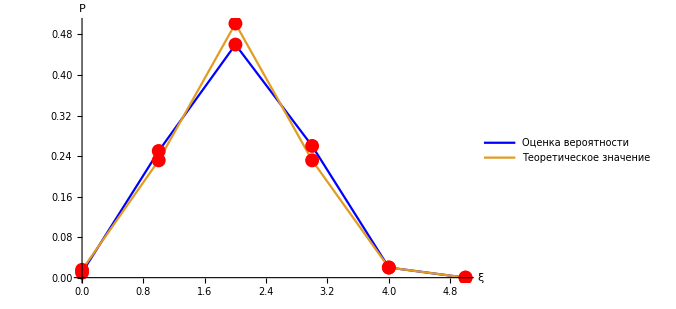

```mathematica
ListPlot[{P,Pteory},PlotRange->All,PlotStyle->{Blue,Thick,PointSize[Large]},AxesStyle->Thick,LabelStyle->Large,AxesLabel->{"ξ","P"},ImageSize->500,Joined->True,Mesh->Full,DataRange->{0,5},MeshStyle->Directive[PointSize[0.02],Red],PlotLegends->{"Оценка вероятности","Теоретическое значение"}]
```